# Comp Bio HW1 - 03 A route to chaos

-Graphics-
Ricker Map, this is what we are looking at in this exercise.
 -Graphics-

## a) Assume that R takes the values from 1 to 30 in steps of 0.1 and plot the bifurcation diagram of η against R as follows. For each value of R, run the model for 300 generations and plot the last 100 values of versus the value of R. The final plot should show the results for all values of R tested. Describe the result.

The term describes the probability of offspring survival

{291,300}

900

0.0909552

{291,100}

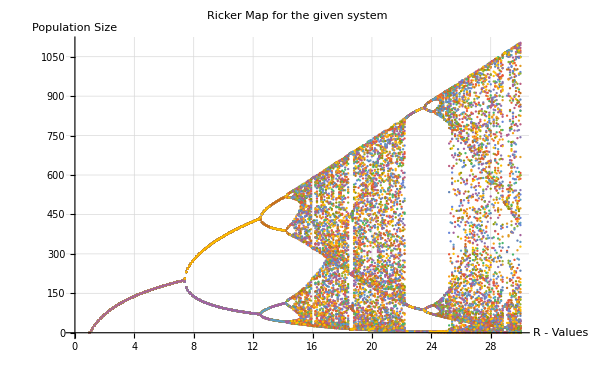

```mathematica
ClearAll["Global`*"];
RValues = Range[1,30,0.1];
alpha = 0.01;
newN[n_] = R * n * Exp[-alpha * n];
n0 = 900;
t0 = 0;
tMax = 299;
numberOfGenerationsOfInterest = 100;


(* Create an empty list to store results for each R *)
resultsSystem = {};

(* Iterate over each R value and store the results in resultsSystem *)
For[R = 1, R <= 30, R += 0.1,
  resultsSystem = Append[resultsSystem, NestList[newN, n0, tMax]];
]

Dimensions[resultsSystem]

(* create a copy of the resultsSystem and kick the first 200 generations out *)
copiedResultsSystem = resultsSystem;

(* Remove the first 200 generations for each R value *)
copiedResultsSystem = Map[Drop[#, 200] &, copiedResultsSystem];

(* Check drop *)
resultsSystem[[1,1]]
copiedResultsSystem[[1,1]]


Dimensions[copiedResultsSystem]

ListPlot[Transpose[copiedResultsSystem][[2 ;;]], 
  DataRange -> {RValues[[1]], RValues[[-1]]},
  ImageSize -> {600, 300},
  GridLines -> Automatic,
  AxesLabel -> {"R - Values", "Population Size"},
  PlotLabel->"Ricker Map for the given system"
  
]
```

The plot above shows how the populations size is developing over the generations. We see that around 65 generations a first bifurcation occurs, where we have one trajectory where the population increases and one where it decreases again

## b) Plot the population dynamics versus τ (where τ = 0, . . . , 40) for four values of R. Choose four representative values of R where has a stable fixed point, a 2-point cycle. a 3-point cycle, and a 4-point cycle. Describe the dynamics observed for the four values of R.

From  the plot in subtask a) we find the following four values of R of interest
- fixed point => R = 5
- 2-point cycle => R = 10
- 3-point cycle => R = 23
- 4-point cycle => R = 13

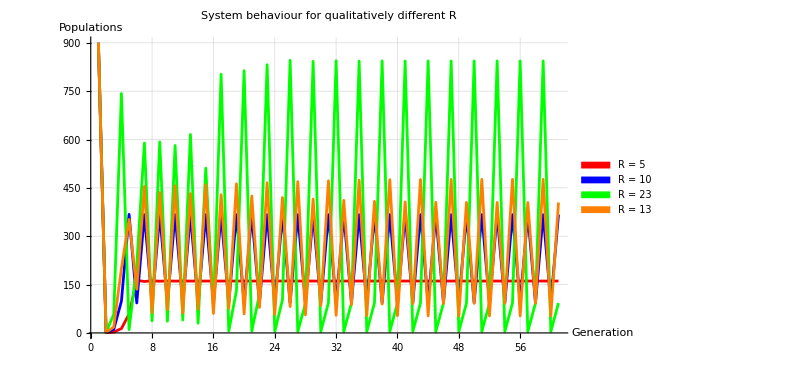

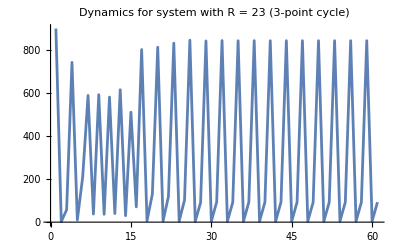

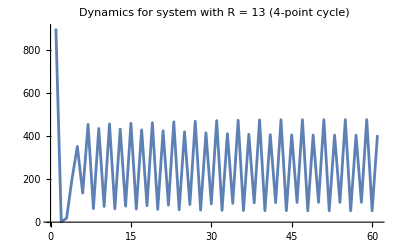

```mathematica
ClearAll["Global`*"];
RValues = {5,10,23,13};
alpha = 0.01;
newN[n_] = R * n * Exp[-alpha * n];
n0 = 900;
t0 = 0;
tMax = 60;
numberOfGenerationsOfInterest = 100;

R = RValues[[1]];
results1 = NestList[newN, n0, tMax];
R = RValues[[2]];
results2 = NestList[newN, n0, tMax];
R = RValues[[3]];
results3 = NestList[newN, n0, tMax];
R = RValues[[4]];
results4 = NestList[newN, n0, tMax];

resultsSystem = {results1, results2, results3, results4};

(* Create a list of plot legends with colors based on RValues *)
colors = {Red, Blue, Green, Orange};
legends = Table[SwatchLegend[{colors[[i]]}, {"R = " <> ToString[RValues[[i]]]}], {i, Length[RValues]}];

plots = Table[
  ListPlot[resultsSystem[[i]], PlotRange -> All, Joined -> True,PlotLegends -> legends[[i]], PlotStyle -> colors[[i]],  AxesLabel-> {"Generation", "Populations"}],
  {i, Length[RValues]}
];

Show[plots, PlotRange -> All, GridLines->Automatic ,ImageSize -> {600, 300}, PlotLabel->"System behaviour for qualitatively different R"]

(* Seperate plot for system 3*) 
ListPlot[results3,
Joined -> True,
PlotLabel->"Dynamics for system with R = 23 (3-point cycle)"]


(* Seperate plot for system 4*) 
ListPlot[results4,
Joined -> True,
PlotLabel->"Dynamics for system with R = 13 (4-point cycle)"]
```

Lets check the four different cases:
Case 1 (R = 5 -> Fixed Point):
As expected the system reaches a fixed point after about 10 generations at a population size of 161 and stays in steady state after this.

Case 2 (R = 10 -> 2-point cycle):
One finds that the population size is either 93 or  and oscillates in between these two cases. The period of this cycle is exactly 2 generations. 

Case 4 (R = 23 -> 3-point cycle):
One finds that the system takes 3 different values



And jump from one to each other in a given sequence: 844 -> 4 -> 93 -> 844 and again
The period of this behaviour is 3 generations.
fixed 
Case 4 (R = 13 -> 4-point cycle):
One finds, that we have a periodic behaviour with 4-points that we oscillate in between. When observing the system for more than 40 generations (as it is defined in the exercise), so for example 60 generations, one finds that the points that the system approaches are




These points are surpassed in a certain order: 477 -> 53 -> 405 -> 92 -> 477 and again
The period of this behaviour is 4 generations.

## c) Investigating the plot in subtask a), at which value R1 of R does the population dynamics bifurcate from a stable equilibrium to a stable 2-point cycle? At which value R2 does the dynamics bifurcate to a stable 4-point cycle?

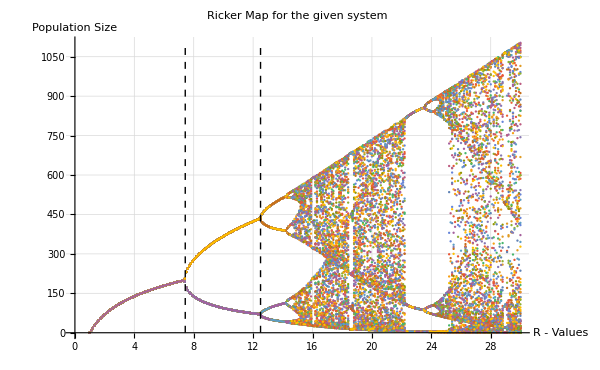

```mathematica
ClearAll["Global`*"];
RValues = Range[1,30,0.1];
alpha = 0.01;
newN[n_] = R * n * Exp[-alpha * n];
n0 = 900;
t0 = 0;
tMax = 299;
numberOfGenerationsOfInterest = 100;


(* Create an empty list to store results for each R *)
resultsSystem = {};

(* Iterate over each R value and store the results in resultsSystem *)
For[R = 1, R <= 30, R += 0.1,
  resultsSystem = Append[resultsSystem, NestList[newN, n0, tMax]];
]

(* create a copy of the resultsSystem and kick the first 200 generations out *)
copiedResultsSystem = resultsSystem;

(* Remove the first 200 generations for each R value *)
copiedResultsSystem = Map[Drop[#, 200] &, copiedResultsSystem];

p1 = 7.43;
p2 = 12.5;

ListPlot[Transpose[copiedResultsSystem][[2 ;;]], 
  DataRange -> {RValues[[1]], RValues[[-1]]},
  ImageSize -> {600, 300},
  GridLines -> Automatic,
  AxesLabel -> {"R - Values", "Population Size"},
  PlotLabel -> "Ricker Map for the given system",
  Epilog -> 
  {Dashed, Line[{{p1, Min[Transpose[copiedResultsSystem][[2 ;;]]]}, {p1, Max[Transpose[copiedResultsSystem][[2 ;;]]]}}],
  {Dashed, Line[{{p2, Min[Transpose[copiedResultsSystem][[2 ;;]]]}, {p2, Max[Transpose[copiedResultsSystem][[2 ;;]]]}}]}}
]
```

Above the plot from subtask a) is reexecuted and two vertical lines (dashed) are added. 
The first vertical line, x = 7.43, is about the point where the bifurcation from the stable fixed point into the 2-point cycle happens.
The second vertical line, x = 12.5, shows the R-value where the bifurcation between the 2-point cycle and the 4-point cycle happens.

## d) By making zooms and refining the R-grid, make a rough estimate of R∞, the first parameter value where the period-doubling bifurcation has repeated an infinite number of times. Explain how you come to this estimate of R∞.

Here we look for 

For this reuse the code from subtask c) and create a manipulate function to move the vertical line. One knows that is reached when an infinite amount of bifurcations happen at this place.
The critical point is approximated with .  
To find this spot my idea was to investigate the trajectories that appear after the bifurcations. Always two trajectories start to form a “bubble” (as in the screenshot below). So when moving from left to the right these bubbles first “open” and then “close”. At the point where they close and infinite amount of period-doublings happen.
-Graphics-

```mathematica
ClearAll["Global`*"];
RValues = Range[1,30,0.1];
alpha = 0.01;
newN[n_] = R * n * Exp[-alpha * n];
n0 = 900;
t0 = 0;
tMax = 299;
numberOfGenerationsOfInterest = 100;

Rstart = 13;
Rstop = 16;
Scaling = 0.005;

(* Create an empty list to store results for each R *)
resultsSystem = {};

(* Iterate over each R value and store the results in resultsSystem *)
For[R = Rstart, R <= Rstop, R += Scaling,
  resultsSystem = Append[resultsSystem, NestList[newN, n0, tMax]];
]

(* create a copy of the resultsSystem and kick the first 200 generations out *)
copiedResultsSystem = resultsSystem;

(* Remove the first 200 generations for each R value *)
copiedResultsSystem = Map[Drop[#, 200] &, copiedResultsSystem];


pInf = 14.78;

Manipulate[
  ListPlot[Transpose[copiedResultsSystem][[2 ;;]], 
    DataRange -> {Rstart, Rstop},
    ImageSize -> {400, 800},
    GridLines -> Automatic,
    AxesLabel -> {"R - Values", "Population Size"},
    PlotLabel -> "Ricker Map to determine the R_inifty bifurcations points",
    AspectRatio-> 2,1
    Epilog -> {
      {Dashed, Line[{{pInf, Min[Transpose[copiedResultsSystem][[2 ;;]]]}, {pInf, Max[Transpose[copiedResultsSystem][[2 ;;]]]}}]}
    }
    ],
  {{pInf, pInf}, Rstart, Rstop, 0.01}
]
```

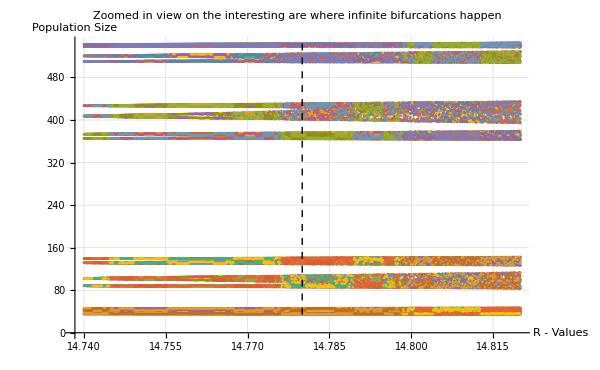

```mathematica
ClearAll["Global`*"];
RValues = Range[1,30,0.1];
alpha = 0.01;
newN[n_] = R * n * Exp[-alpha * n];
n0 = 900;
t0 = 0;
tMax = 299;
numberOfGenerationsOfInterest = 100;

Rstart = 14.74;
Rstop = 14.82;
Scaling = 0.0001;

(* Create an empty list to store results for each R *)
resultsSystem = {};

(* Iterate over each R value and store the results in resultsSystem *)
For[R = Rstart, R <= Rstop, R += Scaling,
  resultsSystem = Append[resultsSystem, NestList[newN, n0, tMax]];
]

(* create a copy of the resultsSystem and kick the first 200 generations out *)
copiedResultsSystem = resultsSystem;

(* Remove the first 200 generations for each R value *)
copiedResultsSystem = Map[Drop[#, 200] &, copiedResultsSystem];

pInf = 14.78;

ListPlot[Transpose[copiedResultsSystem][[2 ;;]], 
    DataRange -> {Rstart, Rstop},
    ImageSize -> {600, 300},
    GridLines -> Automatic,
    AxesLabel -> {"R - Values", "Population Size"},
    PlotLabel -> "Zoomed in view on the interesting are where infinite bifurcations happen",
    Epilog -> {
      {Dashed, Line[{{pInf, Min[Transpose[copiedResultsSystem][[2 ;;]]]}, {pInf, Max[Transpose[copiedResultsSystem][[2 ;;]]]}}]}
    }
   
]
```